```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
$PrePrint=MatrixForm;
```

```mathematica
gamma=-0.0163;
nmax=7;
n=100;
time=100;
steps=1000;
nk=10;

p=2*n*gamma;
y=Table[Sum[If[j+k-q==n,Conjugate[Subscript[a,q][t]]Subscript[a,j][t]Subscript[a,k][t],0],{q,-nmax,nmax}, {j,-nmax,nmax},{k,-nmax,nmax}], {n,-nmax,nmax}];
eqs=Table[I*D[Subscript[a,n][t],t]==n^2*Subscript[a,n][t]+p*y[[n+nmax+1]], {n,-nmax,nmax}];
var=Table[Subscript[a,j], {j,-nmax,nmax}];
ictab=Table[Null, {i,-nmax,nmax}];
ic0=({{0.08201829631602794+0.047317809196744276 ⅈ}, {0.014251371861995887-0.12027794308416526 ⅈ}, {-0.08042013201086406-0.1301082560525131 ⅈ}, {-0.22433886296313693+0.1590104348303842 ⅈ}, {0.015497532109861378+0.26848062265198197 ⅈ}, {0.2937827752112084+0.1586544848332494 ⅈ}, {0.11388745239963204-0.2673708249037954 ⅈ}, {-0.3490172810403259-0.27736077814471505 ⅈ}, {-0.2520444557014234+0.2099847581377048 ⅈ}, {0.12202234302485487+0.3119439217456451 ⅈ}, {0.2760951779976225+0.03594314276989444 ⅈ}, {0.09058946238683178-0.23482051702614182 ⅈ}, {-0.09772147326539571-0.15486263531389327 ⅈ}, {-0.12005664297485667+0.005069795838354757 ⅈ}, {0.020098887536054495+0.03515745225626919 ⅈ}});
```

```mathematica
For[i=1,i<steps+1,i++,
Clear["Subscript"];
(*zadanie war pocz i rozw rnania*)
If[i==1,ic=Table[Subscript[a,j][0]==ic0[[j+nmax+1]], {j,-nmax,nmax}];,ic=Table[Subscript[a,j][0]==ictab[[j+nmax+1]]//.{x_}:>x, {j,-nmax,nmax}] ];
s=NDSolve[{eqs,ic},var, {t,0,time},Method->"ExplicitRungeKutta"];

(*psi^2 i jej pochodne (przeksztalcone)*)
q0[t_,x_]:=Abs[Sum[Subscript[a,j][t]*Exp[I*2*Pi*j*x] /. s, {j,-nmax,nmax}]]^2;q1[t_,x_]:=Re[2*Pi*I*Sum[(j-k)*Subscript[a,j][t]*Conjugate[Subscript[a,k][t]]*Exp[I*2*Pi*(j-k)*x] /. s, {j,-nmax,nmax}, {k,-nmax,nmax}]];
q2[t_,x_]:=Re[-4*Pi^2*Sum[(j-k)^2*Subscript[a,j][t]*Conjugate[Subscript[a,k][t]]*Exp[I*2*Pi*(j-k)*x] /. s, {j,-nmax,nmax}, {k,-nmax,nmax}]];


(*obliczenie tablicy maksimow dla danego kroku (polozenia moge byc poza przeidzalem [0,1]*)
maxtab=Table[Null, {j,0,time*nk}];
initial=Table[q0[0,k/1000]//.{x_}:>x, {k,0,1000}];
xinitial=(Ordering[initial,-1]-1)*0.001;
b2=xinitial//.{x_}:>x;
Do[
b1=b2+0.01;
While[Abs[b1-b2]>0.00001, b1=b2; b2=b1-(q1[j/nk,b1]//.{x_}:>x)/(q2[j/nk,b1]//.{x_}:>x)] ;
maxtab[[j+1]]=b2;, {j,0,time*nk}];



step=Table[maxtab[[i]]-maxtab[[i-1]], {i,2,Length[maxtab]-1}];
If[i==1, steptab=step;, steptab=Join[steptab,step];];
Export["skoki.wdx", steptab];




x1[t]:=Sum[Abs[Subscript[a,j][t]]^2*j^2, {j,-nmax,nmax}];
x2[t]:=Sum[If[q+j==k+l, Conjugate[Subscript[a,q][t]]*Conjugate[Subscript[a,j][t]]*Subscript[a,k][t]*Subscript[a,l][t],0], {q, -nmax,nmax}, {j,-nmax,nmax},{k,-nmax,nmax}, {l,-nmax,nmax}];
x3[t]:=Sum[Abs[Subscript[a,j][t]]^2*j, {j,-nmax,nmax}];
x4[t]:=Sum[Abs[Subscript[a,j][t]]^2, {j,-nmax,nmax}];

ene[t_]:=Evaluate[Re[x1[t]+p/2*x2[t]] /.s];
nall[t_]:=Evaluate[x4[t] /.s];
ped[t_]:=Evaluate[x3[t] /.s];
ekin[t_]:=Evaluate[x1[t] /.s];
eint[t_]:=Evaluate[p/2*x2[t] /.s];

(*Subscript[n,0][t_]:=Evaluate[Abs[Subscript[a,0][t]]^2/.s];*)

If[i==1,e0=ene[0]//.{x_}:>x; n0=nall[0]//.{x_}:>x; p0=ped[0]//.{x_}:>x;];
efl=(ene[0]-e0)/e0;
pfl=(ped[0]-p0)/p0;
nfl=(nall[0]-n0)/n0;


(*Zapis tablicy z nowymi warunkami pocz*)
Do[ictab[[j+nmax+1]]=Subscript[a,j][time] /. s, {j,-nmax,nmax}];
]
```

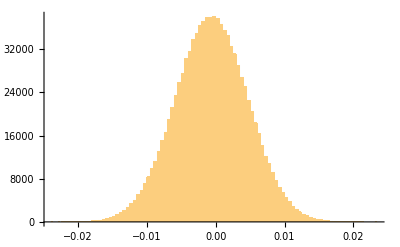

```mathematica
Histogram[steptab,100]
```

```mathematica
Directory[]
```

/home/ml